Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2023/24
F.Javier Muñoz Delgado

# Prácticas y Notas 14: Métodos numéricos para resolver ecuaciones diferenciales.

## Resolución numérica de ecuaciones diferenciales.

En numerosas ocasiones no es posible encontrar la función solución exacta de un problema de valores iniciales.
		y’=f(x,y)
		y(x_0)=y0

En cada punto (x,y) del dominio, f nos da el valor de la derivada de y en el punto x. Resolver una ecuación diferencial sería encontrar una función que en cada punto, x, tome un valor, y, que tenga una derivada que valga f(x,y).

### Campo de direcciones de una ecuación diferencial.

Dada una ecuación diferencial y’=f(x,y), se trata de buscar funciones y(x) que en cada punto (x,y) la derivada y’(x) valga f(x,y). Para tener una idea de cómo son las soluciones podríamos dibujar en una malla de puntos del plano (del tipo (x,y)), vectores de la forma (1,f(x,y)).

```mathematica
Clear[f,x,y]
```

```mathematica
f[x_,y_]:=2x
```

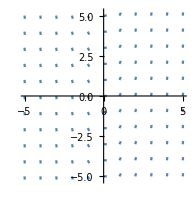

```mathematica
ParametricPlot[Table[{-5+i ,-5+j}+t {1,f[-5+i,-5+j]}/Sqrt[1+f[-5+i,-5+j]^2],{i,0,10},{j,0,10}],{t,0,.2}]
```

Viendo los vectores, vemos que la función debe ser decreciente cuando x es negativa y creciente cuando x es positiva. En este caso sabemos que las soluciones son las primitivas de 2x, es decir las funciones de la forma x^2 + C, con C un número real cualquiera. Si dibujamos los vectores anteriores y unas cuantas funciones soluciones, podremos ver cómo ajustan.

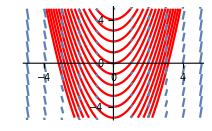

```mathematica
Show[Plot[Table[x^2+i,{i,-10,10}],{x,-5,5},PlotRange->{-5,5},PlotStyle->Red],ParametricPlot[Table[{-5+i ,-5+j}+t {1,f[-5+i,-5+j]},{i,0,10},{j,0,10}],{t,0,.1}]]
```

Las soluciones de la ecuación diferencial son las funciones del tipo y(x)=x^2+C. Vemos en el dibujo cómo encajan los vectores de dirección con las soluciones. 

Hay multitud de ecuaciones diferenciales que no sabemos resolver. El cálculo de primitivas ya aparecía en las ecuaciones diferenciales de la forma y’=f(x), siendo muchas de ellas imposibles de resolver con los métodos estudiados. 

Incluso aunque la función f(x,y) tenga un “aspecto” sencillo, no tenemos garantías de saber resolver la ecuación. Por ejemplo, la ecuación diferencial y’ = x y + y + x.

```mathematica
DSolve[{y'[x]==x y[x]+y[x]+x,y[0]==1},y[x],x]//Simplify
```

{{y[x]→1/2 (-2+4 ⅇ^(1/2 x (2+x))+ⅇ^(1/2 (1+x)^2) √(2 π) Erf[1/(√2)]-ⅇ^(1/2 (1+x)^2) √(2 π) Erf[(1+x)/(√2)])}}

#### Aproximación de las soluciones

Ejemplos como el anterior nos llevan a estudiar métodos numéricos para aproximar las soluciones de una ecuación diferencial.

Cuando tenemos un problema de valores iniciales 
		y’=f(x,y)
		y(x_0)=y0
de la solución que buscamos, y(x) conocemos su valor en x0, y también el valor de su derivada y’(x0), pues basta evaluar f(x0,y0). Incluso, derivando en la ecuación diferencial , podríamos conocer el valor de y’’(x0), y’’’(x0), ...

La interpolación de Taylor nos permite encontrar un polinomio que coincida con la función en un punto, tanto en el valor de la función como en el de sus derivadas consecutivas hasta un cierto orden. En los ejemplos vistos en el tema de interpolación veíamos que la aproximación podía mejorar al utilizar más derivadas. También veíamos que la aproximación era buena si estábamos “cerca” del punto de partida y que podía empeorar si nos alejábamos. 

Por ejemplo, si tenemos el PVI 
	y’=xy+x+y (ecuación diferencial)
	y(0)=1 (condición inicial),
sabemos que la solución y(x) debe cumplir que y(0)=1 (Condición inicial). También que y’(0)=0*y(0)+0+y(0)=1.
Si derivamos en la ecuación diferencial, y’’(x) = 1*y(x)+x*y’(x)+1+y’(x). Con lo que y’’(0)=y(0)+0*y’(0)+1+y’(0)=1+1+1=3.
Si derivamos otra vez,  y’’’(x)=y’(x)+1*y’(x)+x*y’’(x)+0+y’’(x). Por tanto, y’’’(0)=y’(0)+y’(0)+0*y’’(0)+y’’(0)=1+1+0+3=5.

Con estos datos podríamos interpolar la función solución y(x), 1+x+3 x^2/2+5 x^3/6. Este polinomio vale en 0 igual que la función solución, también tiene la misma derivada primera, segunda y tercera en el punto 0. El problema es que si queremos conocer el valor de y(x) en un punto “lejano” del 0, la aproximación puede no ser muy buena. Podríamos calcular más derivadas de y(x) e interpolar con polinomios de Taylor de más grado.

Otra posibilidad es usar el polinomio de Taylor de grado bajo para avanzar una pequeña cantidad y volver a realizar los cálculos aproximados de las derivadas en el nuevo punto.   

	Así, para dar una aproximación de la solución y(x) del problema de valores iniciales en un intervalo [a,b], dividimos en n subintervalos el intervalo [a,b], h= (b-a)/n, x_i= a + i h, (de donde x_0=a, x_n=b). A continuación tratamos de buscar valores aproximados de la función y(x) en esos puntos. Veamos cómo quedarían los métodos según utilicemos polinomios de Taylor de menor o mayor grado. 
	
	
	Para poder ver el comportamiento de los distintos métodos y compararlos vamos a considerar una ecuación diferencial que podamos resolver, y así comparar la solución real y las aproximaciones.

Ejemplo:
y’=sen x cos x - y cos x
y(0)=1 
cuya solución es y(x)=-1 + 2 ⅇ^(-sen x)+ sen x
Trataremos de aproximar la solución y(x) en el intervalo [0,2π]. En particular conocer el valor aproximado que cada método da para y(2π), que sabemos que es 1.

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[x]==Sin[x]* Cos[x]-y[x]*Cos[x],y[0]==1},y[x],x]//Simplify
```

{{y[x]→-1+2 ⅇ^(-Sin[x])+Sin[x]}}

```mathematica
Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}]
```

-Graphics-

En el punto 2π la función vale 1.

```mathematica
-1+2 ⅇ^(-Sin[x])+Sin[x]/.x->2π
```

1

### Método de Euler.

En este método se utiliza el valor de la función y de la derivada en un punto (aunque sean aproximados) para estimar el valor en el siguiente punto.

Así tratamos de obtener los valores {y_i} con i=0,...,n como aproximaciones de {y(a+i*h)} con i=0,...,n con la siguiente fórmula:

y_(i+1)=y_i+h f(x_i, y_i)

```mathematica
Clear["Global`*"]
```

En este caso, la expresión f (x,y) con la que trabajaremos es:

```mathematica
f[x_,y_]:=Sin[x]*Cos[x]-y*Cos[x]
```

Introducimos el intervalo, la condición inicial y el número, n, de particiones. Con eso se calcula el paso h y los puntos intermedios entre a y b.

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

Escribimos la fórmula del Método de Euler:

```mathematica
For[i=0,i≤n,i=i+1,yy[i+1]=yy[i]+h f[xx[i],yy[i]]]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}]//MatrixForm
```

(0. | 1
0.314159 | 0.685841
0.628319 | 0.573252
0.942478 | 0.576946
1.25664 | 0.6198
1.5708 | 0.651958
1.88496 | 0.651958
2.19911 | 0.622922
2.51327 | 0.588558
2.82743 | 0.588754
3.14159 | 0.672335
3.45575 | 0.883555
3.76991 | 1.23988
4.08407 | 1.70439
4.39823 | 2.16852
4.71239 | 2.47137
5.02655 | 2.47137
5.34071 | 2.13911
5.65487 | 1.59472
5.96903 | 1.04001
6.28319 | 0.636945)

Aquí están los valores aproximados de la solución desde x=0, hasta x=2π. En concreto, para para x=2π, tenemos:

```mathematica
{xx[n],yy[n]}
```

{6.28319,0.636945}

Ahora dibujamos los puntos obtenidos y la gráfica de la función solución.

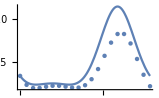

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

Esta es la aproximación de Euler con n=20, aumentando el valor de n podemos conseguir mejorar la aproximación.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]*Cos[x]-y*Cos[x]
```

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=40;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,yy[i+1]=yy[i]+h f[xx[i],yy[i]]]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}];
```

```mathematica
{xx[n],yy[n]}
```

{6.28319,0.804368}

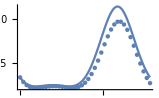

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

Esta es la aproximación de Euler con n=40. Apreciamos que al pasar de n=20 a n=40, los puntos calculados está más cerca de la gráfica. En concreto en el extremo del intervalo, el punto 2π, el valor exacto es 1, la aproximación por Euler con n=20 fue 0.636945 y con n=40 es 0.804368.

### Métodos de Taylor (segundo orden).

Si en lugar de utilizar solo la primera derivada en el punto usásemos más derivadas (aunque sean aproximadas) en cada punto, las aproximaciones que consigamos podrían ser mejores.

Así, si usamos la segunda derivada, trataremos de obtener los valores {y_i} con i=0,...,n como aproximaciones de {y(a+ih)} con i=0,...,n con la siguiente fórmula:

y_(i+1)=y_i+h f(x_i, y_i)+h^2/2(∂_x f(x_i, y_i)+∂_y f(x_i, y_i) f(x_i, y_i))

En nuestro ejemplo:
y’(x)=sen x cos x - y(x) cos x
y(0)=1

Derivando en la expresión de y’(x), obtenemos: 
y’’(x)	=	cos x cos x -sen x sen x - y’(x) cos x + y(x) sen x =
	=	cos^2 x - sen^2 x - (sen x cos x - y(x) cos x) cos x + y(x) sen x =
	=	cos^2 x - sen^2 x - sen x  cos^2 x + y(x)  cos^2 x + y(x) sen x =
	=	cos^2 x (1+y(x)-sen x) + sen x (y-sen x)

Con el Mathematica podemos calcular la derivada segunda de y(x), derivando la función f(x,y).

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]*Cos[x]-y*Cos[x]
```

```mathematica
D[f[x,y],x]+D[f[x,y],y]f[x,y]//Simplify
```

Cos[x]^2 (1+y-Sin[x])+(y-Sin[x]) Sin[x]

```mathematica
seg[x_,y_]:=Cos[x]^2 (1+y-Sin[x])+(y-Sin[x]) Sin[x]
```

```mathematica
a=0.;
b=2π;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:= a+i* h
```

Escribimos la fórmula del Método de Taylor de segundo orden:

```mathematica
For[i=0,i≤n,i=i+1,yy[i+1]=yy[i]+h f[xx[i],yy[i]]+h^2/2 seg[xx[i],yy[i]]]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}];
```

Por último, hacemos un dibujo con los puntos obtenidos y la solución exacta del problema de valores iniciales que, en este caso, es conocido.

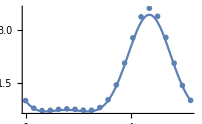

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

Vemos que los puntos están mucho más cerca de la solución con n=20, que los puntos dados por el método de Euler con n=20. En particular el valor aproximado en x=2π es 1.00622 (Mucho más cercano al valor exacto que es 1).

### Métodos de Taylor (tercer orden).

Podríamos seguir usando derivadas de mayor orden.

Así, si usamos también la tercera derivada, trataremos de obtener los valores {y_i} con i=0,...,n como aproximaciones de {y(a+ih)} con i=0,...,n con la siguiente fórmula:

y_(i+1)=y_i+h f(x_i, y_i)+h^2/2(∂_x f(x_i, y_i)+∂_y f(x_i, y_i) f(x_i, y_i))+h^3/(3!)(∂_x f^(1)(x_i, y_i)+∂_y f^(1)(x_i, y_i) f(x_i, y_i)) 

donde  
f^(1)(x_i, y_i)=(∂_x f(x_i, y_i)+∂_y f(x_i, y_i) f(x_i, y_i))

Ejemplo:
y’(x)=sen x cos x - y(x) cos x
y(0)=1

Derivando en la expresión de y’(x), obtuvimos: 
y’’(x)	=	cos^2 x (1+y(x)-sen x) + sen x (y(x)-sen x)

De nuevo podemos volver a derivar esta última expresión para obtener y’’’(x).

Lo haremos con el Mathematica.

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]*Cos[x]-y*Cos[x]
```

```mathematica
D[f[x,y],x]+D[f[x,y],y]f[x,y]//Simplify
```

Cos[x]^2 (1+y-Sin[x])+(y-Sin[x]) Sin[x]

```mathematica
seg[x_,y_]:=Cos[x]^2 (1+y-Sin[x])+(y-Sin[x]) Sin[x]
```

```mathematica
D[seg[x,y],x]+D[seg[x,y],y]f[x,y]//Simplify
```

1/4 Cos[x] (4+2 y-2 (4+y) Cos[2 x]-3 (5+4 y) Sin[x]+Sin[3 x])

```mathematica
ter[x_,y_]:=1/4 Cos[x] (4+2 y-2 (4+y) Cos[2 x]-3 (5+4 y) Sin[x]+Sin[3 x])
```

```mathematica
a=0.;
b=2π;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:= a+i* h
```

Escribimos la fórmula del Método de Taylor de tercer orden:

```mathematica
For[i=0,i≤n,i=i+1,yy[i+1]=yy[i]+h f[xx[i],yy[i]]+h^2/(2!)seg[xx[i],yy[i]]+h^3/(3!)ter[xx[i],yy[i]]]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}];
```

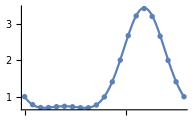

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

Vemos que al aplicar el Método de Taylor de tercer orden, los puntos obtenidos están aún más cerca de la solución. En particular, el error al estimar el valor en x=2π ha pasado de 0.00622 (=|1-1.00622|) en el Método de Taylor de segundo orden a 0.00187(=|1-0.998122|) en el de tercer orden. En Euler (Taylor de primer orden), con el mismo valor de n=20, el error en el extremo era 0.363055 (= |1-0.636945|).

El problema al aumentar las derivadas es que no siempre son fáciles de calcular, y lógicamente, los cálculos realizados tienen un mayor coste.

### Métodos de Runge-Kutta.

Estos métodos proponen mejorar la exactitud utilizando, en lugar de mas derivadas, más evaluaciones de f(x,y) en distintos puntos, antes de estimar y_(i+1). De la familia de métodos de Runge-Kutta, veremos dos métodos con dos evaluaciones y el método clásico que utiliza 4 evaluaciones de f.

#### Métodos de Runge-Kutta (1)

En lugar de utilizar el valor de la derivada en el punto inicial de cada subintervalo y saltar hasta el final, evaluamos f(x,y) en el punto medio del subintervalo, siguiendo la estimación de Euler.

y_(i+1)=y_i+h  k_(i 2)

 {k_(i 1)=f(x_i,y_i)
k_(i 2)=f(x_i+1/2 h,y_i+1/2 h k_(i 1))

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]* Cos[x]-y*Cos[x]
```

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];
k[i,2]=f[xx[i]+h/2,yy[i]+h/2 k[i,1]];
yy[i+1]=yy[i]+h k[i,2] ]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}];
```

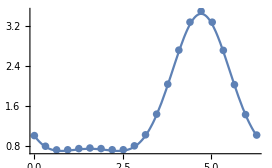

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

#### Métodos de Runge-Kutta (2)

En lugar de utilizar el valor de la derivada en el punto inicial de cada subintervalo y saltar hasta el final, hacemos la media entre la derivada en el punto inicial y en el punto final, siguiendo la estimación de Euler. Con ese valor medio, se avanza hasta el final del subintervalo.

y_(i+1)=y_i+h/2  (k_(i 1)+k_(i 2))

 {k_(i 1)=f(x_i,y_i)
k_(i 2)=f(x_i+h,y_i+h k_(i 1))

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]* Cos[x]-y*Cos[x]
```

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];
k[i,2]=f[xx[i]+h,yy[i]+h k[i,1]];
yy[i+1]=yy[i]+h/2 (k[i,1]+k[i,2])]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}]
```

{{0.,1},{0.314159,0.786626},{0.628319,0.708141},{0.942478,0.704984},{1.25664,0.725602},{1.5708,0.736545},{1.88496,0.726133},{2.19911,0.705546},{2.51327,0.70853},{2.82743,0.788142},{3.14159,1.00601},{3.45575,1.4077},{3.76991,1.98293},{4.08407,2.62772},{4.39823,3.14955},{4.71239,3.3486},{5.02655,3.13989},{5.34071,2.61338},{5.65487,1.9709},{5.96903,1.4023},{6.28319,1.00668}}

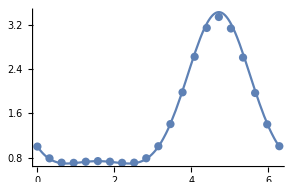

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

#### Métodos de Runge-Kutta (3)

Escribimos la fórmula del Método de Runge-Kutta clásico:

El método de Runge-Kutta clásico utiliza cuatro evaluaciones de f y realiza un promedio. A la evaluación en el primer punto (que se hace en Euler), se añaden dos evaluaciones en el punto central y otra en el final del subintervalo.

y_(i+1)=y_i+h/6  (k_(i 1)+2 k_(i 2)+2 k_(i 3)+k_(i 4))

 {k_(i 1)=f(x_i,y_i)
k_(i 2)=f(x_i+h/2,y_i+h/2 k_(i 1))
k_(i 3)=f(x_i+h/2,y_i+h/2 k_(i 2))
k_(i 4)=f(x_i+h,y_i+h k_(i 3))

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=Sin[x]* Cos[x]-y*Cos[x]
```

```mathematica
a=0.;
b=2Pi;
yy[0]=1;
n=20;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];

k[i,2]=f[xx[i]+h/2,yy[i]+h/2 k[i,1]];

k[i,3]=f[xx[i]+h/2,yy[i]+h/2 k[i,2]];

k[i,4]=f[xx[i]+h,yy[i]+h k[i,3]];
yy[i+1]=yy[i]+h/6 (k[i,1]+2k[i,2]+2k[i,3]+k[i,4 ])]
```

```mathematica
yy[n]
```

1.00002

```mathematica
sol[x_]:=-1+2 ⅇ^(-Sin[x])+Sin[x]
```

```mathematica
puntos=Table[{xx[i],yy[i]},{i,0,n}]
```

{{0.,1},{0.314159,0.777382},{0.628319,0.698931},{0.942478,0.699645},{1.25664,0.723768},{1.5708,0.73581},{1.88496,0.723768},{2.19911,0.699646},{2.51327,0.698933},{2.82743,0.777388},{3.14159,1.00002},{3.45575,1.41514},{3.76991,2.01214},{4.08407,2.68226},{4.39823,3.22568},{4.71239,3.4364},{5.02655,3.22567},{5.34071,2.68224},{5.65487,2.01211},{5.96903,1.41512},{6.28319,1.00002}}

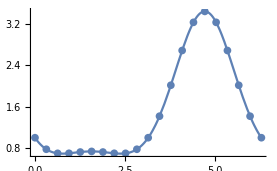

```mathematica
Show[ListPlot[puntos,PlotStyle->PointSize[0.02]],Plot[-1+2 ⅇ^(-Sin[x])+Sin[x],{x,0,2Pi}],PlotRange->All]
```

Comparativa de los métodos vistos. Colocamos los valores que hemos obtenidos por los distintos métodos con n=20.

```mathematica
Transpose[{{0.,0.3141592653589793,0.6283185307179586,0.9424777960769379,1.2566370614359172,1.5707963267948966,1.8849555921538759,2.199114857512855,2.5132741228718345,2.827433388230814,3.141592653589793,3.4557519189487724,3.7699111843077517,4.084070449666731,4.39822971502571,4.71238898038469,5.026548245743669,5.340707511102648,5.654866776461628,5.969026041820607,6.283185307179586},{1,0.6858407346410207,0.5732521254805015,0.5769458676740765,0.6197997002688043,0.6519582948012947,0.6519582948012947,0.6229216743755132,0.5885576507104869,0.5887539636350062,0.6723346750772585,0.883554842674898,1.2398752920251435,1.7043938333838549,2.1685157100935935,2.4713655036364823,2.4713655036364823,2.1391148849826638,1.594718208751519,1.0400127261680363,0.6369452871449723},{1,0.7845367786519143,0.7155716948206107,0.7232260832617722,0.7512296585518828,0.7650212039848584,0.7534254651882898,0.7287449800563701,0.7263981037750422,0.8024242961418349,1.0240295590711432,1.4456197882755306,2.0660738468013453,2.7816161212120276,3.3795728511815466,3.6218639750004304,3.393784129855928,2.7932558299908337,2.062717370777326,1.4300910388792434,1.0062164508493063},{1,0.7793690658718643,0.7007145148234463,0.7004562454819593,0.7235300883221748,0.734579452947322,0.7214814739506686,0.6960444477496329,0.6936094689693244,0.7700278259877543,0.9908993491602389,1.4056142184101494,2.004211862154386,2.676339158322766,3.2183171828280535,3.422338968539679,3.2041052878046385,2.659336992266867,1.9953784310682596,1.407055805757729,0.9981218878222726},{1,0.786989298449351,0.7137645115871185,0.7158419426703155,0.7395978749535275,0.7512859238457433,0.7396678474982634,0.7166196609463478,0.7168377882616985,0.7950041205141217,1.0156747236633277,1.4288746350496386,2.0285964913477614,2.710177675864107,3.270140128299989,3.48946232528889,3.269431248743035,2.7052662149399875,2.0193067661029502,1.4197259293245974,1.0107926160320393},{1,0.7866260627402508,0.7081410965158943,0.7049843605773023,0.7256015276297544,0.736545174997966,0.7261327352931054,0.705546171914894,0.7085297878839062,0.788142470762418,1.0060076060181715,1.4076992625816607,1.9829313055102378,2.6277216619964823,3.1495522232826993,3.348596903139162,3.139890539592478,2.6133844231899195,1.9709036401947027,1.402296088082819,1.006684762654146},{1,0.7773818379252144,0.6989305962587367,0.6996448985576348,0.7237677755806863,0.7358097719036916,0.7237680201227807,0.6996463828348961,0.6989332269895044,0.7773882290124129,1.0000211701409907,1.4151374055281702,2.0121390367934477,2.6822609603192475,3.225675594452896,3.4363992103251326,3.225673298765985,2.6822449124859586,2.0121106674946576,1.4151161196775668,1.0000178506335948},{1.,0.7773535807529408,0.6988979329709661,0.6996081527909879,0.723721798356248,0.7357588823428847,0.7237217983562481,0.6996081527909879,0.698897932970966,0.7773535807529408,0.9999999999999999,1.4151540418225264,2.012209662316393,2.6823817380290365,3.2258293783705794,3.43656365691809,3.2258293783705803,2.6823817380290373,2.012209662316394,1.4151540418225268,1.0000000000000002}}]//MatrixForm
```

(0. | 1 | 1 | 1 | 1 | 1 | 1 | 1.
0.314159 | 0.685841 | 0.784537 | 0.779369 | 0.786989 | 0.786626 | 0.777382 | 0.777354
0.628319 | 0.573252 | 0.715572 | 0.700715 | 0.713765 | 0.708141 | 0.698931 | 0.698898
0.942478 | 0.576946 | 0.723226 | 0.700456 | 0.715842 | 0.704984 | 0.699645 | 0.699608
1.25664 | 0.6198 | 0.75123 | 0.72353 | 0.739598 | 0.725602 | 0.723768 | 0.723722
1.5708 | 0.651958 | 0.765021 | 0.734579 | 0.751286 | 0.736545 | 0.73581 | 0.735759
1.88496 | 0.651958 | 0.753425 | 0.721481 | 0.739668 | 0.726133 | 0.723768 | 0.723722
2.19911 | 0.622922 | 0.728745 | 0.696044 | 0.71662 | 0.705546 | 0.699646 | 0.699608
2.51327 | 0.588558 | 0.726398 | 0.693609 | 0.716838 | 0.70853 | 0.698933 | 0.698898
2.82743 | 0.588754 | 0.802424 | 0.770028 | 0.795004 | 0.788142 | 0.777388 | 0.777354
3.14159 | 0.672335 | 1.02403 | 0.990899 | 1.01567 | 1.00601 | 1.00002 | 1.
3.45575 | 0.883555 | 1.44562 | 1.40561 | 1.42887 | 1.4077 | 1.41514 | 1.41515
3.76991 | 1.23988 | 2.06607 | 2.00421 | 2.0286 | 1.98293 | 2.01214 | 2.01221
4.08407 | 1.70439 | 2.78162 | 2.67634 | 2.71018 | 2.62772 | 2.68226 | 2.68238
4.39823 | 2.16852 | 3.37957 | 3.21832 | 3.27014 | 3.14955 | 3.22568 | 3.22583
4.71239 | 2.47137 | 3.62186 | 3.42234 | 3.48946 | 3.3486 | 3.4364 | 3.43656
5.02655 | 2.47137 | 3.39378 | 3.20411 | 3.26943 | 3.13989 | 3.22567 | 3.22583
5.34071 | 2.13911 | 2.79326 | 2.65934 | 2.70527 | 2.61338 | 2.68224 | 2.68238
5.65487 | 1.59472 | 2.06272 | 1.99538 | 2.01931 | 1.9709 | 2.01211 | 2.01221
5.96903 | 1.04001 | 1.43009 | 1.40706 | 1.41973 | 1.4023 | 1.41512 | 1.41515
6.28319 | 0.636945 | 1.00622 | 0.998122 | 1.01079 | 1.00668 | 1.00002 | 1.)

En la primera columna aparecen los puntos (de 0 a 2π) y en la última los valores exactos de la solución. El resto de columnas, de izquierda a derecha, son: los valores de Euler, Taylor de segundo orden, Taylor de tercer orden, Runge-Kutta en el punto medio, Runge-Kutta en los extremos y Runge-Kutta clásico. Este último método da los valores más próximos a la solución, aunque es el que más evaluaciones de f realiza.

## Enero 22 Aula de Informática 3.- Aproximar el valor de la solución de la ecuación diferencial y’ = xy - 3x -1, con la condición inicial y(0)=0, en el punto x=2, utilizando el método de Runge-Kutta clásico con paso h=0.25 . 1) -21.6113, 2) -30.4484, 3) -39.2854, 4) -36.8355, 5) -27.9985

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]:=x*y-3x-1
```

```mathematica
a=0.;
b=2.;
yy[0]=0;
n=8;
h=(b-a)/n;
xx[i_]:=a+i*h;
```

```mathematica
For[i=0,i≤n,i=i+1,
k[i,1]=f[xx[i],yy[i]];

k[i,2]=f[xx[i]+h/2,yy[i]+(h/2)k[i,1]];

k[i,3]=f[xx[i]+h/2,yy[i]+(h/2)k[i,2]];

k[i,4]=f[xx[i]+h,yy[i]+h k[i,3]];
yy[i+1]=yy[i]+(h/6) (k[i,1]+2k[i,2]+2k[i,3]+k[i,4 ])]
```

```mathematica
yy[n]
```

-27.9985

## ENERO 21 13.- Dada la ecuación diferencial y’(x) = x y(x) + x + 2 junto con la condición inicial y(0)=1, utilizar el método de Euler para aproximar y(2) con paso 1.

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = x y(x) + x + 2; con f(x,y) = x y + x + 2.
El punto inicial es x_0= 0, la condición inicial es y(x_0)= y_0 = 1, el paso es h=1 (para en dos pasos, llegar desde el 0 al 2).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=0, y_0 = 1, 
x_1= x_0 + h = 0 + 1 = 1; y_1= y_0+ h f(x_0,y_0) = 1 + 1*f(0,1) = 1 + (0*1 + 0 + 2)=3.
x_2= x_1 + h = 1 + 1 = 2; y_2= y_1+ h f(x_1,y_1) = 3 + 1*f(1,3) = 3 + (1*3 + 1 + 2)=9.

De esta forma, y(2) ≃ y_2=9.

## JUNIO 21 13.- Dada la ecuación diferencial y’(x) = y(x) + x + 2 junto con la condición inicial y(1)=1, utilizar el método de Euler para aproximar y(3) con paso 1.

Solución:
En el método de Euler, aproximamos los valores de la función solución de la ecuación diferencial utilizando el valor de la derivada.

La ecuación diferencial es y’(x)=f(x,y), en este caso es y’(x) = y(x) + x + 2; con f(x,y) = y + x + 2.
El punto inicial es x_0= 1, la condición inicial es y(x_0)= y_0 = 1, el paso es h=1 (para en dos pasos, llegar desde el 1 al 3).
x_n = x_0 + n h, y_n= y_(n-1)+ h f(x_(n-1),y_(n-1))

Calculamos x_0=1, y_0 = 1, 
x_1= x_0 + h = 1 + 1 = 2; y_1= y_0+ h f(x_0,y_0) = 1 + 1*f(1,1) = 1 + (1 + 1 + 2)=5.
x_2= x_1 + h = 2 + 1 = 3; y_2= y_1+ h f(x_1,y_1) = 5 + 1*f(1,5) = 5 + (5 + 2 + 2)=14.

De esta forma, y(3) ≃ y_2=14.

## ENERO 19 PRÁCTICAS 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+y+1 con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(1):

Solución: Seguimos lo visto en clase.
y’ = f(x,y) (en este caso f(x,y)= x^2+y-1), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) 
Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x^2+y+1
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",N[y0,20]],{2}]
```

En 0.5 vale aprox. 2.3444

En 1. vale aprox. 4.87111

```mathematica
N[y0,10]
```

4.87111

```mathematica
4.8711090087890625
```

## ENERO 19 PRÁCTICAS 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x+y con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(1):

Solución: Seguimos lo visto en clase.
y’ = f(x,y) (en este caso f(x,y)= x+y), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4)
Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x+y
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 1.79688

En 1. vale aprox. 3.43469

## ENERO 19 PRÁCTICAS 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x+y-1 con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5 Aproximación de y(1):

Solución: Seguimos lo visto en clase.
y’ = f(x,y) (en este caso f(x,y)= x+y-1), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4)
Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x+y-1
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 1.14844

En 1. vale aprox. 1.71735

## ENERO 19 PRÁCTICAS 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+y-1 con la condición y(0)=1, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(1):

Solución: Seguimos lo visto en clase.
y’ = f(x,y) (en este caso f(x,y)= x^2+y-1), y(x_0)= y_0 (en este caso x_0=0, y_0=1)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x^2+y-1
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h];y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{2}]
```

En 0.5 vale aprox. 1.04753

En 1. vale aprox. 1.43642

## ENERO 18 Dada la ecuación diferencial y’(x) = 3 x y(x) + 2 junto con la condición inicial y(0)=1, utilizar el método de Euler para aproximar y(1) con paso 0.5.

Solución: 
Conocemos el valor y(0) (por ser la condición inicial). Como nos piden aproximar y(1) con paso 0.5, tendremos que aplicar dos veces el método de Euler, del 0 al 0.5 y del 0.5 al 1.
y’(x) = 3 x y(x) + 2
y(0)=1

f(x,y)=3xy+2
x_0=0
y_0=1
h=0.5
x_n= x_0+ nh

y(0.5)  ≃  y_1 = y_0 + h f(x_0,y_0) = 1 + 0.5 f(0,1) = 1 + 0.5*(3*0*1+2) = 2
y(1)  ≃  y_2 = y_1 + h f(x_1,y_1) = 2 + 0.5 f(0.5, 2) = 2 + 0.5*(3*0.5*2+2) = 2+2.5 = 4.5

## ENERO 18 PRÁCTICAS 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=2 x^2+y^2 con la condición y(0)=1, en el punto 2, utilizando el método de Runge-Kutta con paso h=0.5. Aproximación de y(2):

Solución: Seguimos lo visto en clase.
y’ = f(x,y) (en este caso f(x,y)= 2 x^2+y^2), y(x_0)= y_0 (en este caso x_0=0, y_0=1)

y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4)
Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= 2x^2+y^2
```

```mathematica
x0=0;
y0=1;h=0.5;Do[k1=f[x0,y0];k2=f[x0+h/2,y0+k1 h/2];k3=f[x0+h/2,y0+k2 h/2];k4=f[x0+h,y0+k3 h]; y0=y0+h(k1+2k2+2k3+k4)/6; x0=x0+h;Print["En " ,x0," vale aprox. ",y0],{4}]
```

En 0.5 vale aprox. 2.12227

En 1. vale aprox. 32.1378

En 1.5 vale aprox. 4.19311×10^15

En 2. vale aprox. 1.13402×10^241

## JUNIO 18 PRÁCTICAS 6.- Calcular una aproximación de la solución y(x), de la ecuación diferencial y’=x^2+xy+1 con la condición y(0)=M, en el punto 1, utilizando el método de Runge-Kutta con paso h=0.25. M=dígito del DNI Aproximación de y(1):

Solución: Seguimos lo visto en clase.
y’ = f(x,y) (en este caso f(x,y)= x^2+x y+1), y(x_0)= y_0 (en este caso x_0=0, y_0=M)
y_(n+1) = y_n + 1/6h (k_1+2 k_2+ 2 k_3 + k_4) Donde
k_1=f(x_n,y_n)
k_2=f(x_n+1/2h,y_n + 1/2k_1h)
k_3=f(x_n+1/2h,y_n + 1/2k_2h)
k_4=f(x_n+h,y_n+k_3h)

```mathematica
Clear[f,x]
```

```mathematica
f[x_,y_]:= x^2+x*y+1
```

```mathematica
x0=0;
y0=7;h6=0.25;Do[k1=f[x0,y0];k2=f[x0+h6/2,y0+k1 h6/2];k3=f[x0+h6/2,y0+k2 h6/2];k4=f[x0+h6,y0+k3 h6];y0=y0+h6(k1+2k2+2k3+k4)/6; x0=x0+h6;Print["En " ,x0," vale aprox. ",y0],{4}]
```

En 0.25 vale aprox. 7.48274

En 0.5 vale aprox. 8.51967

En 0.75 vale aprox. 10.3391

En 1. vale aprox. 13.3623